# Lista 3 - Introdução à Física Computacional I

## Marcos Vinícius Rodrigues Ribeiro

Problema 1.1

Definindo a funcão enunciada:

```mathematica
f[a_][x_]:=a*Sin[Pi*x];
```

Em seguida uso a função “Show” para gerar as curvas e utilizar de funções que alteram visualmente o gráfico. Foi utilizada a “PlotLegends”  para gerar a legenda das curvas, a “PlotStyle” para a cor de cada curva e “FrameLabel” para nomear os eixos e “LabelStyle” para tamanho da fonte e a cor das letras.

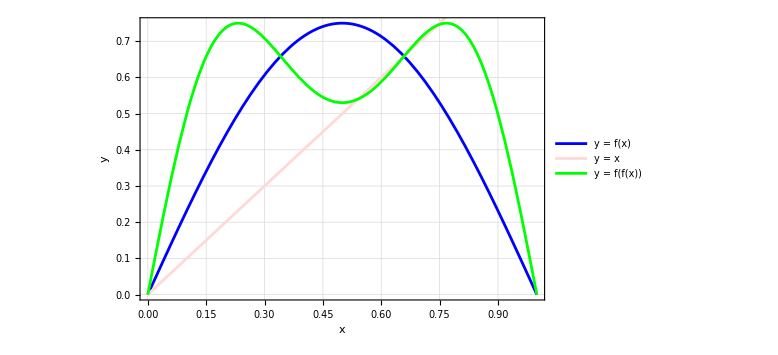

```mathematica
Show[Plot[f[0.75][x],{x,0,1},PlotLegends->{"y = f(x)"},PlotStyle->Blue,Frame->True,FrameLabel->{"x","y","Funções para a = 0.75"},LabelStyle->{FontSize->14,Black},ImageSize->Large,GridLines->Automatic],Plot[x,{x,0,1},PlotStyle->LightRed,PlotLegends->{"y = x"}],Plot[f[0.75][f[0.75][x]],{x,0,1
},PlotStyle->Green,PlotLegends->{"y = f(f(x))"}]]
```

Com base no gráfico gerado, é possível observar que as curvas azul e verde coincidem em dois pontos, sendo um deles x = 0, e o outro um ponto fixo x = x*. Logo, há indícios de ser um ciclo dois, onde a cada duas aplicações o valor de x se repete.

Problema 1.2

Defino a função “pontos” através da função “Compile” como sugerido pelo problema. As variáveis que essa função recebe são: “a”, que é o coeficiente da função ; “m” é o n.08úmero de iterações que serão descartadas; e . Tal qual mostrado em aula, a partir de um valor de “a”, é produzido uma lista de “m” pontos produzidos por “n” aplicações. 
Na prática, será aplicada a função “NestList” uma quantidade “n” de vezes na função iterativa que está sendo o objeto de estudo.  A função “Drop” descartará os “m” primeiros elementos da lista denominada “xlista”, que são elementos da lista de iterações e compõem o transiente que leva aos atratores (pontos fixos, ciclos 2, ciclos 4 etc.).  Esse processo é feito para diversos  valores de “a”. Por fim, as duplas de valores são armazenados na lista “saida”. A função “Module” foi utilizada para gerar o ambiente onde as variáveis são definidas sem interferir no restante do código, tanto neste item quanto nos itens desenvolvidos mais à frente.

```mathematica
pontos:=Compile[{a,{m,_Integer},{n,_Integer}},
Module[{xlista,saida},xlista=Drop[NestList[a*Sin[Pi*#]&,0.5,n],m+1];
saida={};
(*Este laço itera sobre os elementos de xlista e anexa pares de valores de "a" e dos pontos fixos encontrados*)
Do[AppendTo[saida,{a,xlista[[i]]}],{i,1,Length[xlista]}];
(*Retornar a lista de saída*)saida],{{saida,_Real,2}}]
```

Defino a função “varrepontos” através da função “Compile”, que receberá o intervalo varrido de valores de “a”e os valores “m” e “n” que são utilizados na função “pontos”. 
Em seguida, defino a função “diagbifurca”, que gera o gráfico do mapa logístico, onde recebe os mesmo argumentos da função ”varrepontos”. A função Flatten é utilizada para nivelar a lista de listas resultante. Novamente fiz uso de funções para fins estéticos do gráfico.

```mathematica
varrepontos:=Compile[{amin,amax,na,{m,_Integer},{n,_Integer}},Module[{grandelista},
grandelista={};
(*Este laço itera sobre os valores de "a" e anexa as listas resultantes da função pontos ao grandelista*)
Do[AppendTo[grandelista,pontos[a,m,n]],{a,amin,amax,(amax-amin)/na}];
(**)
Flatten[grandelista,1]],{{grandelista,_Real,3}}]
```

```mathematica
diagbifurca[amin_,amax_,na_,m_,n_]:=ListPlot[varrepontos[amin,amax,na,m,n],Axes->False,Frame->True,FrameLabel->{"a","x"},PlotStyle->PointSize[0.001],AspectRatio->1,ImageSize->Large]
```

```mathematica
grafico = diagbifurca[0,1,1000,1024,1024+512]
```

-Graphics-

Como pode ser observado no gráfico, dado o valor de a = 0.75, há duas curvas geradas após uma bifurcação em aproximadamente a = 0,725. As conclusões tiradas do item anterior são confirmadas através do mapa de bifurcações.

Problema 1.3

Neste item, chamo diversas vezes a função “diagbifurca” para observação do mapa logístico e estimativa do chute. Com o chute em mente, nomeio “est`n`” com n = {2, 4, 8, 16, 32, 64, 128} para cada dupla de estimativas de “x” e “a” dado um dos “n”. 
Utilizo a função do Mathematica “FindRoot”, onde, no primeiro argumento, vão as duas equações que tem ser satisfeitas, no segundo argumento a variável para qual quero encontrar o valor junto de seu chute inicial, por fim, no terceiro argumento é inserido a segunda variável e seu chute.

```mathematica
Show[diagbifurca[0.6,0.9,1000,1024,1024+512],PlotRange->{0.3,0.9}]
```

-Graphics-

```mathematica
est2=FindRoot[{x==Nest[f[a],x,2],D[Nest[f[a],x,2],x]==-1},{{x,0.44},{a,0.83}}]
```

{x→0.444794,a→0.833266}

```mathematica
Show[diagbifurca[0.85,0.87,1000,1024,1024+512],PlotRange->{0.3,0.45}]
```

-Graphics-

```mathematica
est4=FindRoot[{x==Nest[f[a],x,4],D[Nest[f[a],x,4],x]==-1},{{x,0.37},{a,0.85}}]
```

{x→0.373868,a→0.858609}

```mathematica
Show[diagbifurca[0.863,0.866,1000,1024,1024+512],PlotRange->{0.35,0.40}]
```

-Graphics-

```mathematica
est8=FindRoot[{x==Nest[f[a],x,8],D[Nest[f[a],x,8],x]==-1},{{x,0.358},{a,0.864}}]
```

{x→0.358643,a→0.864084}

```mathematica
est16=FindRoot[{x==Nest[f[a],x,16],D[Nest[f[a],x,16],x]==-1},{{x,0.3596},{a,0.8652}}]
```

{x→0.359673,a→0.865259}

```mathematica
Show[diagbifurca[0.8654,0.8658,1000,1024,1024+512],PlotRange->{0.354,0.362}]
```

-Graphics-

```mathematica
est32=FindRoot[{x==Nest[f[a],x,32],D[Nest[f[a],x,32],x]==-1},{{x,0.3585},{a,0.8655}}]
```

{x→0.35851,a→0.865511}

```mathematica
est64=FindRoot[{x==Nest[f[a],x,64],D[Nest[f[a],x,64],x]==-1},{{x,0.3588},{a,0.865562}}]
```

{x→0.358805,a→0.865565}

```mathematica
est128=FindRoot[{x==Nest[f[a],x,128],D[Nest[f[a],x,128],x]==-1},{{x,0.358665},{a,0.865575}}]
```

{x→0.358652,a→0.865576}

Agrupo as estimativas no conjunto “aestimativas”.

```mathematica
{est2[[2]],est4[[2]],est8[[2]],est16[[2]],est32[[2]],est64[[2]],est128[[2]]}
```

{a→0.833266,a→0.858609,a→0.864084,a→0.865259,a→0.865511,a→0.865565,a→0.865576}

Problema 1.4

A constante de Feigenbaum é obtida a partir da razão entre a diferença dos coeficientes de “a” de um ciclo para outro, vide:

δ_j=(a_j-a_(j-1))/(a_(j+1)-a_j)

```mathematica
δ2=((a/.est4)-(a/.est2))/((a/.est8)-(a/.est4))
δ3=((a/.est8)-(a/.est4))/((a/.est16)-(a/.est8))
δ4=((a/.est16)-(a/.est8))/((a/.est32)-(a/.est16))
δ5=((a/.est32)-(a/.est16))/((a/.est64)-(a/.est32))
δ6=((a/.est64)-(a/.est32))/((a/.est128)-(a/.est64))
```

4.62871

4.66052

4.66735

4.6688

4.66912

Há um indicio forte de que os valores estão tendendo ao valor da constante δ = 4.669201609.

Problema 1.5

Calculando as diferenças entres os valores obtidos e o valor de refe.08rência. Com isso, tenho um conjunto de duplas, dos valores calculados e sua flutuação em relação ao valor original. Com isso, gera-se um gráfico com um ajuste indicado pelo enunciado. Utilizei o “FindFit” para encontrar o ajuste, seu primeiro argumento é onde fica endereçado o conjunto de dados, o segundo argumento é a forma da função que é desejado ajustar os dados e o último argumento é a variável.

```mathematica
δlog=4.669201609;
Δ3=δlog-δ3;
Δ4=δlog-δ4;
Δ5=δlog-δ5;
Δ6=δlog-δ6;
dadosj={{3,Δ3},{4,Δ4},{5,Δ5},{6,Δ6}}
```

{{3,0.00868539},{4,0.00185001},{5,0.000397075},{6,0.0000849162}}

Por fim, o gráfico foi gerado com a função “Show” que exibe o gráfico gerado pela função “Plot” junto dos dados, que vão no segundo argumento da função. A função que gera o gráfico utiliza o ajuste encontrado pela “FindFit” e em seu segundo argumento há o intervalo no qual será feito a curva. Novamente foram usadas funções para estética.

{c1→0.896967,c2→1.5458}

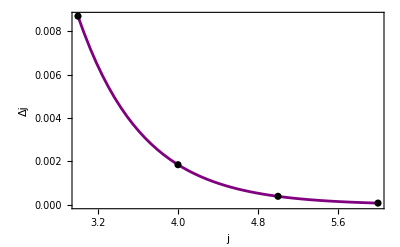

```mathematica
FindFit[dadosj,c1*Exp[-c2*j],{c1,c2},j]
Show[Plot[0.8969668397489078*Exp[-1.5457970335516942*j],{j,3,6},PlotStyle->Purple,Frame->True,FrameLabel->{"j","Δj"}],ListPlot[dadosj,PlotStyle->Black]]
```

Finalmente, o gráfico sugere uma grande tendência de Δ_jse aproximar de 0 quando j >>1. Logo, δ_j tende ao valor exato da constante de Feigenbaum δ_log= 4.669201609.

Problema 1.6

Defino a função lyanpunovC, como a apresentada na aula 12, uma função compilada usando a função “Compile” que calcula o expoente de Lyapunov para o mapa logístico. Ela recebe os parâmetros: “a” parâmetro do mapa logístico; “x0” é a condição inicial; “n” é o número total de iterações; já o “m” é o número de iterações a serem descartadas antes de calcular o expoente.

```mathematica
lyapunovC=Compile[{a,x0,{n,_Integer},{m,_Integer}},
xlista=Drop[NestList[a*Sin[Pi*#]&,x0,n],m+1];
Total[Log[Abs[a*Pi*Cos[Pi*xlista]]]]/Length[xlista]];  (*xlista armazena as iterações do mapa logístico,começando com a condição inicial x0*)
```

```mathematica
NumberForm[lyapunovC[1,0.5,10000,1000],3]
```

0.691

A função compilada é utilizada na produção de um gráfico para visualizar como o expoente de Lyapunov varia com o parâmetro “a”. Os eixos são definidos como “a” (eixo x) e “Expoente de Lyapunov” (eixo y).

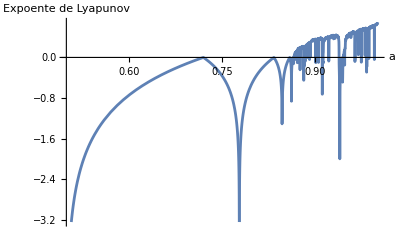

```mathematica
Plot[lyapunovC[a,0.5,10000,1000],{a,0.5,1},AxesLabel-> {"a","Expoente de Lyapunov"}]
```

O mapa exibe um comportamento caótico a partir de a = 0.86, apesar de eventualmente apresentar “ilhas de estabilidade”, indicadas pelos expoentes negativos repentinos.

Problema 2.1

Defino a função discreteMapIteration que realiza a iteração do mapa enunciado. A função recebe: “α” que é o parâmetro que será iterado, recebe a condição inicial representada como uma lista {x, y} “xy0”; recebe o número de iterações “n” e recebe o número de iterações que serão descartadas “m”.  A  função retorna uma lista contendo coordenadas (x, y) resultantes da iteração do mapa.  Se algumas condições iniciais resultarem em divergência dos pontos iterados, mensagens de erro podem ser geradas durante a execução. Essas mensagens podem ser ignoradas, pois a lista resultante será utilizada para a visualização do gráfico. Novamente  a função “Module”, neste item e nos seguintes.

```mathematica
IteraMapa[alfa_,xy0_,n_,m_]:=Module[{x,y,xn1,yn1,lista},{x,y}=xy0;
lista={};(* lista que armazenará os pontos *)
Do[xn1=x*Cos[alfa]-(y-x^2)*Sin[alfa];
yn1=x*Sin[alfa]+(y-x^2)*Cos[alfa];
x=xn1;
y=yn1;
If[i>=m,AppendTo[lista,{x,y}];],{i,1,n+m}];
lista]
```

Problema 2.2

A função “varrePontosMapa” é definida para varrer as condições iniciais e gerar os gráficos. A entradas da função são: “α” que é o parâmetro que será iterado;  número de iterações “n”; o número de iterações que serão descartadas “m”.  A função utilizada para gear os gráficos é a “ListPlot”, que gera um gráfico a partir de uma lista de valores. Foi usada “PlotStyle” para definir o tamanho do ponto; “AxesLabel” para nomear os eixos;  “AspectRatio” para a saída não distorcer o formato do gráfico.

```mathematica
varrePontosMapa[alpha_,n_,m_]:=Module[{condIniciais,trajetorias},condIniciais=Tuples[Range[-1,1,0.25],2];
trajetorias=IteraMapa[alpha,#,n,m]&/@condIniciais;
(*Visualizando a lista de listas*)
ListPlot[trajetorias,PlotStyle->PointSize[Tiny],AxesLabel->{"x","y"},AspectRatio->1,ImageSize->Large]]
```

Problema 2.3

Neste item foi chamada a “varrePontosMapa” para os valores do enunciado. Foi utilizado a função “Off” para impedir a saída do aviso de erro sobre excesso de número de iterações. OBS: esse item demora até 10 minutos para rodar e gerar os gráficos.

```mathematica
alfa1=ArcCos[0.24];
alfa2=ArcCos[0.22];
n=2000;
m=1000;

varrePontosMapa[alfa1,n,m]
varrePontosMapa[alfa2,n,m]

Off[General::ovfl]
Off[$IteratioLimit::itlim]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

-Graphics-

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

-Graphics-

Problema 3.1

```mathematica
F[x_][t_][w_]:=m*x''[t]==-(k*x[t])+(a*(1-x[t]^2)*x'[t])+(F0*Cos[w*t]);
```

Foi definida a função “resolve” para obter as soluções da EDO, que recebe: tempo inicial “tmin”; tempo máximo “tmax”; “x0” é a posição inicial; “v0” é a velocidade inicial; “w” é a frequência. É utilizado a função “NDSolve” para resolver a EDO numericamente e “ParametricPlot” para gerar o gráfico da solução. Também foi incluída funções para a parte visual do gráfico.

```mathematica
resolve[tmin_,tmax_,x0_,v0_,w_]:=
(
sol=NDSolve[{F[x][t][w]/.{m->1,k->1,a->3,F0->5},x[0]==x0,x'[0]==v0},x,{t,tmin,tmax}];ParametricPlot[{x[t],x'[t]}/.sol,{t,tmin,tmax},AxesLabel->{"x","v"},PlotRange->All,PlotLabel->Row[{"w=",w}]]
)
```

Foi feito um laço com a função “Do” para percorrer os valores de “w” pedidos no enuciado.

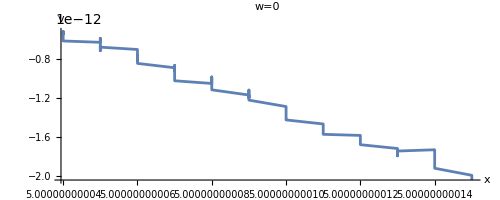

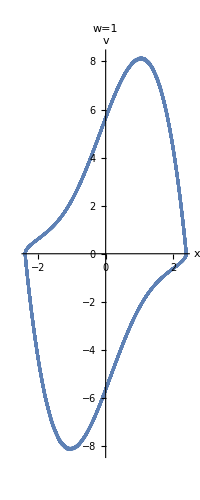

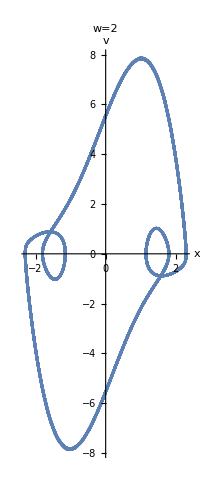

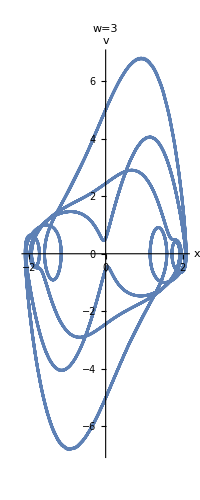

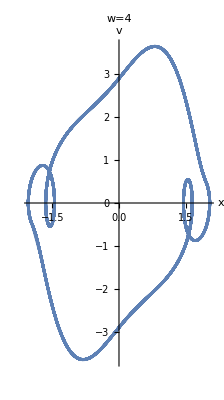

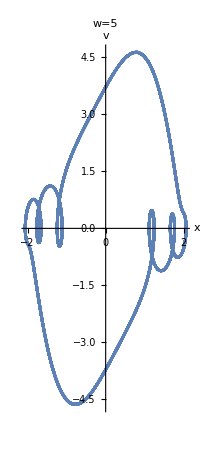

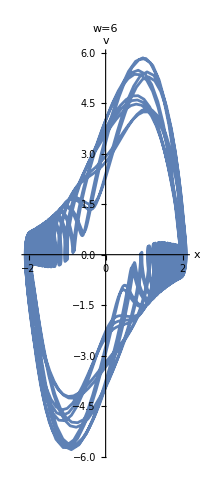

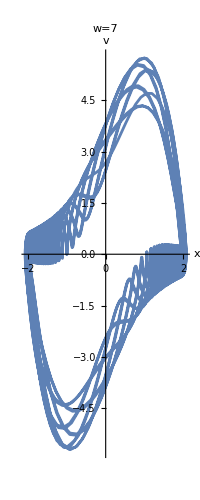

```mathematica
Do[Print[resolve[1900,2000,0,0,w]],{w,0,10}]
```

Observa-se que, até w=5, a solução da equação de van der Pol indica ser periódica. Já para w>5, é apresentado um comportamento caótico.

Problema 3.2

Foi definida a função “pontos”, que recebe: “w” frequência; “n” número de iterações; “ndesc” iterações que serão descartadas; “xx” ponto inicial; “vv” velocidade inicial. A função devolve um lista com elementos de 3 componentes.

```mathematica
pontos2[w_,n_,ndesc_,xx_,vv_]:=Module[{T,x0,v0,ponto,lista},
(T=2π/w ;
x0=xx; 
v0=vv; 
lista={};
Do[(ponto={x[T],x'[T]}/.NDSolve[{F[x][t][w]/.{m->1,k->1,a->3,F0->5},x[0]==x0,x'[0]==v0},x,{t,0,T}][[1]];x0=ponto[[1]]; 
v0=ponto[[2]];
If[i>ndesc,AppendTo[lista,{w,x0,v0}]] ),{i,1,n} ];lista) ]
```

Aqui foi utilizada a função “varrepontos” idêntica a da aula. Que produzirá os valores finais de “x” e “v” a partir das força F0. Novamente a função Flatten é utilizada para nivelar a lista de listas resultante.

```mathematica
varrepontos2[wmin_,wmax_,nw_,n_,ndesc_,xx_,vv_]:=Module[{x,v,lista,grandelista},
(x=xx;
v=vv; 
grandelista={}; 
Do[(lista=pontos2[w,n,ndesc,x,v];
AppendTo[grandelista,lista[[All,{1,2}]]];
x=lista[[-1,2]];  
v=lista[[-1,3]]),{w,wmin,wmax,(wmax-wmin)/(nw-1)}];
Flatten[grandelista,1])]
diagbifurca2[wmin_,wmax_,nw_,n_,ndesc_,xx_,vv_]:=
ListPlot[varrepontos2[wmin,wmax,nw,n,ndesc,xx,vv],Axes->False,Frame->True,FrameLabel->{"w","x"},PlotStyle-> PointSize[0.001],AspectRatio->1]
```

Chamo a “diagbifurca2”, que usa  a “ListPlot” para plotar a lista devolvida por “varrepontos2”. O input é o mesmo da “varrepontos2” e mais dois valores: “wmin” é a frequência mínima e “wmax” que é a frequência máxima percorrida.

```mathematica
diagbifurca2[1,6,500,1024+512,1024,1,0]
```

-Graphics-

Problema 3.3

```mathematica
poincare[w_,n_,ndesc_,tam_]:=Module[{T,x0,v0,ponto,lista},
(T=2π/w;
x0=1; 
v0=0; 
lista={}; 
Do[ (ponto={x[T],x'[T]}/.NDSolve[{F[x][t][w]/.{m->1,k->1,a->3,F0->5},x[0]==x0,x'[0]==v0},x,{t,0,T}][[1]];x0=ponto[[1]]; 
v0=ponto[[2]]; 
If[i>ndesc,AppendTo[lista,ponto]] ),{i,1,n} ];
ListPlot[lista,Axes->False,Frame->True,FrameLabel->{"x","v"},PlotStyle->PointSize[tam],AspectRatio->1]) ]
```

```mathematica
poincare[1.788,2^11+2^9,2^9,0.002]
```

$Aborted

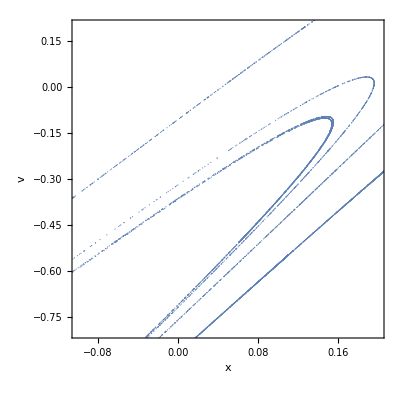

```mathematica
Show[poincare[1.788,2^16+2^11,2^11,0.002],PlotRange->{{-0.1,0.2},{-0.8,0.2}}]
```

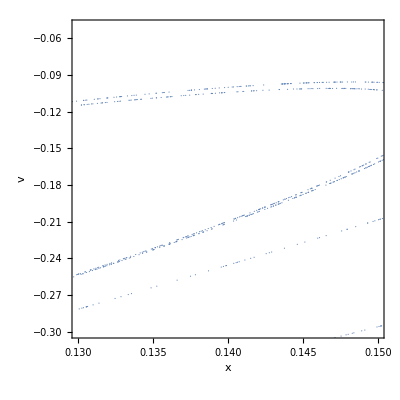

```mathematica
Show[poincare[1.788,2^16+2^11,2^11,0.002],PlotRange->{{0.13,0.15},{-0.3,-0.05}}]
```

Aproximando apenas uma pequena porção do gráfico, é possível identificar uma invariância de escala, característica fractal.

Problema 3.4

Defino a função soluciona que recebe a posição inicial e a velocidade inicial para resolver numericamente a EDO.

```mathematica
soluciona[x0_,v0_]:=NDSolve[{m*x''[t]==-(k*x[t])+(a*(1-x[t]^2)*x'[t])+(F0*Cos[w*t])/.{F0->5,m->1,k->1,a->3,w->1.788},x[0]==x0,x'[0]==v0},x,{t,5,55}]
```

```mathematica
x1=soluciona[0.4,0.1];
x2=soluciona[0.4+10^-8,0.1];
```

Inicio duas listas para armazenar os valores de posição (listax) e de tempo(listat).

```mathematica
listax={};
listat={};
Do[AppendTo[listax,Log[Abs[(x[t]/.x2)-(x[t]/.x1)]]],{t,5,55}]
Do[AppendTo[listat,t],{t,5,55}]
```

```mathematica
dados=Transpose[{listat,Flatten[listax]}];
```

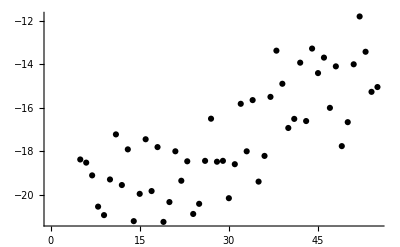

```mathematica
ListPlot[dados,PlotStyle->Black]
```

Após plotar os dados com “ListPlot”, utiliza-se a função “FindFit” utilizando o ajuste indicado pelo enunciado.

```mathematica
s=FindFit[dados,c+(a*t),{c,a},t]
```

{c→-21.1234,a→0.124041}

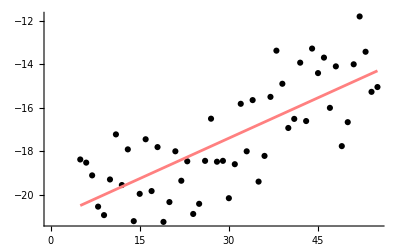

```mathematica
Show[ListPlot[dados,PlotStyle->Black],Plot[c+(a*t)/.s,{t,5,55},PlotStyle->Pink]]
```

O expoente de Lyapunov tem o valor de a = 0.124041, sendo positivo, sinal esperado para um sistema caótico, sensível às condições iniciais, como previsto para w = 1.788.